# Lecture 11 - Potential Problems

### A Puzzle...

An infinite sheet lies in the x-y plane with uniform surface charge density σ. Define the potential to be 0 along the x-y plane.

What is the potential at all points in space?

Using this setup, explain why we cannot set the potential to be 0 at infinity when a charge distribution goes out to infinity?
Note: Because of this fact, we cannot use the formula ϕ=∫kⅆq/r for infinite charge distributions.

Solution
1. By symmetry, the potential can only depend on z and not on x or y. For z>0, the electric field is the constant value

(E⃗)_above=σ/(2 ϵ_0)ẑ

Therefore, the electric potential at a distance z above the x-y plane equals

ϕ=-∫E⃗·ⅆ s⃗
=-∫_0^z (σ/(2 ϵ_0))ⅆz
=-σ/(2 ϵ_0)z

where we have used the displacement vector ⅆ s⃗=ẑ ⅆz. As expected, if σ>0 then the electric field above the charged plane points in the ẑ direction, and hence the potential decreases for larger z. By symmetry, the potential for z<0 is given by ϕ=-σ/(2 ϵ_0)(-z). More compactly, the potential everywhere is given by

ϕ=-σ/(2 ϵ_0)|z|

Notice that the potential is continuous, even though the electric field is discontinuous at the sheet of charge. This is because the electric potential is the integral over the electric field, and the line integral of a function does not change if finitely many points of that point are changed (although the derivative of ϕ is discontinuous when crossing the charged plane).

2. Now consider what the potential is at infinity. According to Equation (TextNumbered), if we travel to infinity in either direction along the z-axis, we find lim_(z→∞) ϕ=-∞ (assuming σ>0). On the other hand, if we stick to the x-y plane (z=0) and go out to infinity in any direction, the potential is equal to 0. When the charge distribution is infinitely large, the potential at infinity is no longer unique. Therefore, we cannot assign infinity any self-consistent value, and so we have to pick another point as our reference point for potential. □

### Work to Assemble Charge Distribution from Infinity

You are given a set of point charges q_j with j=1,2...N with each point charge fixed in place. How much work does it take to assemble this charge distribution (starting from all of the charges being infinitely separated)?

The potential energy of two charges q_j and q_k separated by a distance r_(j,k) is (k q_j q_k)/(r_(j,k)), so the potential energy of the full charge distribution is given by

U=1/2∑_(j=1)^N ∑_(k≠j) (k q_j q_k)/(r_(j,k))

where the factor of 1/2 accounts for the fact that we considered each pair twice in our summation (and the k≠j notation means that you sum from k=1 to k=N but skipping over k=j, since we do not want to count the potential energy of a point charge from itself).

Another way to calculate this quantity is to use the electric potential. Recall that the potential at a distance r from a point charge q equals (k q)/r, so that if we define ϕ_j as the potential at the location of the point charge q_j from all of the other point charges (i.e. ϕ_j=∑_(k≠j) (k q_k)/(r_(j,k))), then

U=1/2∑_(j=1)^N ϕ_j q_j

For a charge distribution ρ, this result generalizes to

U=1/2∫ϕ ⅆq

where we integrate over infinitesimal elements of a charge distribution, where each element has charge ⅆq. For 3D charge distributions, this results in

U=1/2∫ϕ ρⅆv

As a minor mathematical point, although technically we need to define ϕ here as the potential due to all of the charges except those at the point of integration, this altered definition of ϕ will not change the integral. For completeness, we can write the formula for sheets of charge

U=1/2∫ϕ σⅆa

or lines of charge

U=1/2∫ϕ λⅆs

#### Computing the Energy in a Charge Distribution

Note that we now have two distinct ways to compute the energy of a charge distribution, and we will use both in the following example. The first is to consider each bit of charge ⅆq being brought in from infinity to its appropriate location, computing the work done on that charge (ϕ ⅆq) given the partial charge distribution already made, and summing over the entire process. Note that after we have constructed the charge distribution, no charges are moving...so where is the work used to make the charge distribution stored?

The answer is that the energy is stored in the electric field (or equivalently, in the electric potential). Therefore, a second method to determine the work required to create a charge distribution is to ignore the process of creating the distribution, but instead fast-forward to the already-complete charge distribution and analyze the electric field (or electric potential). Equation (TextNumbered) tells us that the energy is given by 1/2∫ϕ ⅆq. Alternatively, we could compute the energy by integrating over the electric field over all space ϵ_0/2∫E^2 ⅆv (see Section 1.15 in the textbook).

### Problems

#### Building a Spherical Shell of Charge

Example
How much work does it take to assemble a spherical shell of charge with radius R and a total charge Q spread evenly over the surface?

Solution
Recall that the electric field outside of a spherical shell with uniform charge distribution and total charge Q is identical to the electric field from a point charge Q at the center of the sphere, namely, E⃗=(k Q)/r^2 r̂. This implies that the potential outside the sphere (given by ϕ=-∫E⃗·ⅆ s⃗) is also the same for both setups outside the spherical shell, namely ϕ=(k Q)/r for r>R. At the surface of the spherical shell, r=R and hence ϕ=(k Q)/R. We will solve for the energy to build the sphere in several ways:

Method 1: Integrate over ϕ of the built sphere
Assume that the sphere has been assembled, so that its potential equals ϕ=(k Q)/R everywhere on its surface. We can directly apply Equation (TextNumbered) to obtain the work required to assemble this spherical shell,

U=1/2∫ϕ ⅆq
=1/2∫(k Q)/R ⅆq
=(k Q)/(2R) ∫ⅆq
=(k Q^2)/(2R)

Method 2: Integrate over E⃗ of the built sphere
We can similarly find the work of a charge distribution by integrating U=ϵ_0/2∫E^2 ⅆv across all space. Note that E⃗=OverVector[0] inside the shell, so we only need to integrate outside the shell where E⃗=(k Q)/r^2 r̂ and E^2=E⃗·E⃗=(k^2 Q^2)/r^4. The full integral in spherical coordinates becomes

U=ϵ_0/2∫E^2 ⅆv
=ϵ_0/2∫_0^(2π) ∫_0^π ∫_0^R (k^2 Q^2)/r^4 r^2 Sin[θ]ⅆrⅆθⅆϕ
=ϵ_0/2 k^2 Q^2 (-1/r)_(r=R)^(r=∞)(-Cos[θ])_(θ=0)^(θ=π)(2π)
=2π ϵ_0(k^2 Q^2)/R
=(k Q^2)/(2R)

Method 3: Calculate the work required to bring every charge onto the sphere
Suppose our sphere is initially an uncharged spherical scaffold of radius R. We will bring in charge from infinity, bit by bit, and smear it evenly on the surface of the sphere until the total charge reaches Q. We will compute the work required to carry out this assembly process.

Assume that at some intermediate stage, the sphere has charge q, and we want to bring in the next bit of charge ⅆq. The energy required to bring this ⅆq from infinity to the surface of the sphere is, by definition, ϕ[r=R]ⅆq where ϕ[r=R]=(k q)/R is the potential at the surface of the sphere. Note that in bringing in this small bit of charge, we had to do work on ⅆq (since it is repelled by the sphere and we moved it in from infinity), but we did not do any work on the spherical shell since it staid in place.

Having brought ⅆq to the surface of the spherical shell, we now want to evenly smear that bit of charge out onto the surface of the sphere. Because the electric field lines point radially away from the spherical shell, moving perpendicularly to these field lines takes zero work, so we can smear out the charge evenly at no extra cost, increasing the total charge on the sphere to q+ⅆq. (Note that because the charge is infinitesimally small, we do not need to worry about the charge exerting force on itself during this smearing process, since all such forces will be of order (ⅆq)^2 which is negligible.)
Therefore, the work required to build the entire sphere is given by

U=∫ϕ ⅆq
=∫_0^Q (k q)/R ⅆq
=k/R ∫_0^Q q ⅆq
=(k Q^2)/(2R)

as found above. □

As a fun aside, it is instructional to verify that the potential at the surface of the spherical shell is ϕ=(k Q)/R by direct integration. We center the spherical shell at the origin and using spherical coordinates to compute ϕ at the point (0,0,R) on the z-axis. The distance r to an infinitesimal area element at coordinates (θ,ϕ) is given by the Law of Cosines as

r=(R^2+R^2-2(R)(R)Cos[θ])^(1/2)
=R (2-2Cos[θ])^(1/2)
=R (2-2(1-2 Sin[θ/2]^2))^(1/2)
=R (4 Sin[θ/2]^2)^(1/2)
=2R Sin[θ/2]

Therefore, the potential at the top point of the spherical shell is given by

ϕ=∫(k ⅆq)/r
=∫(k σⅆa)/r
=∫_0^(2π) ∫_0^π (k σ (R^2 Sin[θ]ⅆθⅆϕ))/(2R Sin[θ/2])
=2π k σ R∫_0^π (Sin[θ]ⅆθ)/(2 Sin[θ/2])
=2π k σ R∫_0^π (2Sin[θ/2]Cos[θ/2]ⅆθ)/(2 Sin[θ/2])
=2π k σ R∫_0^π Cos[θ/2]ⅆθ
=2π k σ R (2Sin[θ/2])_(θ=0)^(θ=π)
=4π k σ R
=(k Q)/R

where in the last step we used σ=Q/(4π R^2). This integral may seem long, but the steps are all straightforward (provided that you remember your trig identities).

#### Dividing the Charge

Example
Consider two spheres, of radii R_1 and R_2, held so far apart from one another that each one negligibly feels the electric field from the other sphere. We want to divide a total amount of charge Q between the two spheres (assume the charge will be distributed evenly on each sphere). How should the charge be divided so as to make the potential energy of the resulting charge distribution as small as possible?

Solution
To answer this, we will first calculate the potential energy of the system for an arbitrary division of the charge, Q_1 on one sphere and Q−Q_1 on the other. Then minimize the energy as a function of Q_1. Assume that any charge put on one of these spheres distributes itself uniformly over the surface of the sphere, the other sphere being far enough away so that its influence can be neglected.

The energy from a sphere of radius R with charge Q_1 uniformly spread over it equals

U_sphere=1/2∫ρ ϕ ⅆv=1/2 Q_1 ((k Q_1)/R)=(k Q_1^2)/(2R)

(Alternatively, we could have used the formula U=ϵ_0/2∫E^2 ⅆv where the integral covers all space. I invite you to verify that this yields the same answer.) Therefore, the total energy from putting charge Q_1 on the sphere with radius R_1 and Q-Q_1 on the sphere with radius R_2 equals

U_tot=(k Q_1^2)/(2 R_1)+(k (Q-Q_1)^2)/(2 R_2)

Differentiating with respect to Q_1 and setting it equal to 0,

0=(ⅆ U_tot)/(ⅆ Q_1)=(k Q_1)/R_1-(k (Q-Q_1))/R_2

which yields

Q_1=R_1/(R_1+R_2)Q

Therefore, we place charge R_1/(R_1+R_2)Q on the sphere with radius R_1 and R_2/(R_1+R_2)Q on the sphere with radius R_2 to minimize their energy. For example, if we set R_1=R_2, then we get the expected result that the charge will be equally distributed between the two spheres.

Note that the second derivative (ⅆ^2 U_tot)/(ⅆ q^2)=k/R_1+k/R_2>0, which shows that this solution is indeed a local minima, and therefore a stable configuration.

Notice that the potentials on the surfaces of the two spheres are (k Q_1)/R_1=(k Q)/(R_1+R_2) and (k (Q-Q_1))/R_2=(k Q)/(R_1+R_2), so the potential difference between the two spheres is zero. In other words, these two spheres could be connected by a wire, and there would still be no redistribution. This is a special example of a very general principle we shall meet in Chapter 3: on a conductor, charge distributes itself so as to minimize the total potential energy of the system. □

#### Center vs. Corner of a Square

Example
A square sheet has side length L and uniform surface charge density σ.

Determine an integral expression for the potential ϕ_center of the square at its center and the potential ϕ_corner at one of its corners

Without explicitly computing the integrals for ϕ_center and ϕ_corner, determine the ratio ϕ_center/ϕ_corner

Solution
At the center of the square, we set up our coordinates as follows

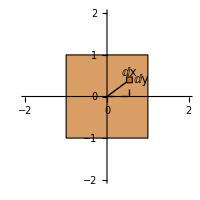

```mathematica
ft=12;a=0.07;b=0.07;centerPlot@Show[Plot[0,{x,-2,2},PlotStyle->None,PlotRange->{{-2,2},{-2,2}},AspectRatio->1,AxesStyle->FontSize->0.01,ImageSize->200],Graphics[{EdgeForm[Black],FaceForm[Lighter@RGBColor[0.772079, 0.431554, 0.102387]],Rectangle[{-1,-1},{1,1}],Line[{{0,0},0.88{0.55,0.4}}],{FaceForm[RGBColor[0.772079, 0.431554, 0.102387]],Rectangle[{0.55,0.4}-{a,b},{0.55,0.4}+{a,b}]},Dashed,Line[{{{0,0},{0.55,0}},{{0.55,0},{0.55,0.8*0.4}}}],Text[Style["ⅆx",ft],{0.55,0.58}],Text[Style["ⅆy",ft],{0.85,0.4}]}]]
```

Therefore, the potential equals

ϕ_center=∫(k ⅆq)/r=∫_(-L/2)^(L/2) ∫_(-L/2)^(L/2) (k σⅆxⅆy)/((x^2+y^2)^(1/2))

On the other hand, if we want to compute the potential at the corner, we would setup our coordinates as follows (you could also setup an equivalent integral in any other corner and obtain the same answer)

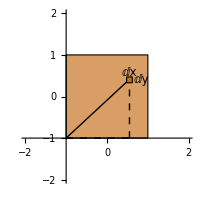

```mathematica
ft=12;a=0.07;b=0.07;
centerPlot@Show[Plot[0,{x,-2,2},PlotStyle->None,PlotRange->{{-2,2},{-2,2}},AspectRatio->1,AxesStyle->FontSize->0.01,AxesOrigin->{-1,-1},ImageSize->200],Graphics[{EdgeForm[Black],FaceForm[Lighter@RGBColor[0.772079, 0.431554, 0.102387]],Rectangle[{-1,-1},{1,1}],Line[{{-1,-1},0.88{0.55,0.4}}],{FaceForm[RGBColor[0.772079, 0.431554, 0.102387]],Rectangle[{0.55,0.4}-{a,b},{0.55,0.4}+{a,b}]},Dashed,Line[{{{-1,-1},{0.55,-1}},{{0.55,-1},{0.55,0.8*0.4}}}],Text[Style["ⅆx",ft],{0.55,0.58}],Text[Style["ⅆy",ft],{0.85,0.4}]}]]
```

Now the integral follows as

ϕ_corner=∫(k ⅆq)/r=∫_0^L ∫_0^L (k σⅆxⅆy)/((x^2+y^2)^(1/2))

These integrals are tough to compute, but we can nevertheless find ϕ_center/ϕ_corner, which we will do in three different ways.

Method 1 (Geometry)
Consider a square with side length 2L. The potential ϕ_corner^(2L) at the center of this large square will be 4 ϕ_corner^(L) by the Principle of Superposition (since this charge configuration is equivalent to four squares of side length L put together). To find the potential at the corner, note that ϕ_corner∝Q/L (since there are no other charges or length scales in the problem) and Q∝σ L^2 so that ϕ_corner∝L. Therefore, ϕ_corner^(2L)=2 ϕ_corner^(L), and so the ratio of the potential at the center to that at the corner equals ϕ_center^(2L)/ϕ_corner^(2L)=(4 ϕ_corner^(L))/(2 ϕ_corner^(L))=2. Note that this is independent of L, so this result holds regardless of the side length of the square.

Method 2 (Algebra)
As an alternative (but equivalent argument), we can also relate the two integrals in Equations (TextNumbered) and (TextNumbered) above. We begin by rewriting Equation (TextNumbered) as

ϕ_center=4∫_0^(L/2) ∫_0^(L/2) (k σⅆxⅆy)/((x^2+y^2)^(1/2))

To bring Equation (TextNumbered) to this same form, we define two new variables x̃=x/2 and ỹ=y/2 so that 2ⅆ x̃=ⅆx and 2ⅆ ỹ=ⅆy. In terms of these new variables, x∈[0,L] and y∈[0,L] translate into x⃗∈[0,L/2] and ỹ∈[0,L/2]. Thus we can rewrite Equation (TextNumbered) as

ϕ_corner=∫_0^(L/2) ∫_0^(L/2) (k σ (2ⅆ x̃)(2ⅆ ỹ))/((4(x̃)^2+4(ỹ)^2)^(1/2))=2∫_0^(L/2) ∫_0^(L/2) (k σ ⅆ x̃ⅆ ỹ)/(((x̃)^2+(ỹ)^2)^(1/2))

Therefore, ϕ_center=2 ϕ_corner.

Method 3 (Mathematica)
Of course, it never hurts to double check this answer using Mathematica to explicitly compute the integrals,

```mathematica
Integrate[(k σ)/(√(x^2+y^2)),{x,-L/2,L/2},{y,-L/2,L/2},Assumptions->L>0]
Integrate[(k σ)/(√(x^2+y^2)),{x,0,L},{y,0,L},Assumptions->L>0]
```

4 k L σ ArcSinh[1]

2 k L σ ArcSinh[1]

So once again we find that ϕ_center=2 ϕ_corner, as desired. □

#### Infinite Sheet - Cutoff Potential

Example
Consider the electric field E⃗ due to an infinite sheet with uniform surface charge density σ. We have already found E⃗ using Gauss’s Law. Find E⃗ again by calculating the potential and then taking the derivative.

You will find that the potential (relative to infinity) due to an infinite sheet diverges. So instead find the potential due to a very large but finite disk with radius R, at a point lying on the perpendicular line through the center. Use a Taylor series to simplify the potential, and then take the derivative to find E. Explain why this procedure is valid, even though it cuts off an infinite amount from the potential.

Solution
As was done in the book (Section 2.6), center the disk around the origin so that it lies in the x-z plane.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

The potential at a distance y along the perpendicular axis is found by breaking the circle into rings,

ϕ=∫_0^R (k (2π r ⅆr σ))/((r^2+y^2)^(1/2))=2π σ k ((r^2+y^2)^(1/2))_(r=0)^(r=R)=σ/(2 ϵ_0) ((R^2+y^2)^(1/2)-y)

The potential along the y-direction equals

E_y=σ/(2 ϵ_0)(1-y/((R^2+y^2)^(1/2)))

Assuming y≪R, we can take the Taylor series to see what the electric field will look like from an infinite sheet,

E_y≈σ/(2 ϵ_0)(1-y/R+O[y/R]^2)=σ/(2 ϵ_0)+O[y/R]

Mathematically, we are done, since in the limit R→∞ only this lowest order term will survive. To finish off the argument, we note that by the symmetry of the situation, the electric field must point away from the sheet of charge, so only E_y should be non-zero for any point in space. And this same argument could be applied to any point, so that E_y=σ/(2 ϵ_0) is the electric field from a sheet of charge.

You may be wondering why our cutoff assumption is valid, since we are neglecting an infinite amount of charge. The validity of this assumption rests on the fact that Equation (TextNumbered) becomes ϕ≈σ/(2 ϵ_0) (R-y) for large R, which is linear in R and causes the potential to go to infinity as R→∞. However, the electric field -(∂ϕ)/(∂y) does not change (in other words, the potential is increased as R increases, but it is increased uniformly at every point in space (that is the same thing as redefining the 0 point of gravitational potential energy to by 5 meters off the ground instead of at ground level; the potential energy of all particles will change, but none of the physics will change because only differences in potential energy matter)). □